```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<"ACPackages`"
<<"ErrorBarPlots`"
```

```mathematica
$WD=SetWorkDir[];
```

```mathematica
$WD=NotebookDirectory[];
```

```mathematica
SetWorkDir["/2006.07.20/Re=10"];
```

```mathematica
(*Table of results: list of {date(year,month,day),mesh(Nx=Nz,Ny),Re,r/R,lfi,F(r),Coriolis,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mϕ,δmϕ,comment}*)
indepkol=10;
depkol=14;
```

## Добавление записей

```mathematica
dvx=dvy=dvz=0;
dqvx=dqvy=dqvz=0;
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={1 10^-8,1 10^-6,1 10^-8,5 10^-7,2 10^-6,1 10^-7};
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={0,4 10^-7,0,0,2 10^-8,0};
```

```mathematica
putlist=Join[{2008,05,14},{10,5},{Rm=2,kappa=0.25,lfi=1,Fr=1,Coriolis=0,mvx,dvx,mvy,dvy,mvz,dvz,qvx,dqvx,qvy,dqvy,qvz,dqvz,Max[Abs[ψ]],Max[Abs[ψ2-ψ1]],"ErrScale 1e-4"}]/.b_:>CForm[b]/;NumericQ[b]
```

{2008,5,14,10,5,1,0.25,1,1,0,0.0034773,1.e-8,0.99565,1.e-6,0.002059,1.e-8,0.001633746976438374,5.e-7,0.584343908857404,2.e-6,0.0009543500669088886,1.e-7,0.0010577742727272744,0.0005478525454545467,ErrScale 1e-4}

```mathematica
putlist>>>($WD<>"\\result.dat")
{Rm,kappa,lfi,Fr,Coriolis,mvx,dvx,mvy,dvy,mvz,dvz,dqvx,qvx,dqvy,qvy,dqvz,qvz,ψ,ψ2,ψ1}=.
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Анализ записей

### Функции

```mathematica
UpdateData:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList["result.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\result.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
MakeRule[el_]:=MapThread[Rule,{fields,el}];
```

```mathematica
ShowDependance[param_,funcs_,conditions_:{}]:=Block[{allbut=GetResults[conditions],dep,deplist,numpar,othern,otherv},If[FreeQ[Drop[fields,{indepkol+1,-2}],param],Print["Wrong parameter"];Return[]];numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];Print["All such parameters=",Union[(#1⟦numpar⟧&)/@allbut]];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
(*Print["dep=",dep];*)
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];Print[otherv];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];Print["Plots can be shown for parameters:"];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;If[Length[dep]>1,nom=Input["Введите номер желаемой зависимости"],nom=1];Print["So constant parameters are:"];Print["\t",Thread[otherv->List@@First[dep⟦nom⟧]]];deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[dep⟦nom⟧]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
GetResults[conditions_:{}]:=Block[{pattern,rules=Union[Select[conditions,Head[#]==Rule&]],
(*Unequal doesn't work always*)
ineqs=And@@Flatten[Select[conditions,MemberQ[{Less,LessEqual,Greater,GreaterEqual,Unequal},Head[#]]∨#==False&]]},
MatchesQ[el_]:=Module[{mr=MakeRule[el]},Simplify[ineqs/.mr]∧Complement[rules,mr]=={}];
Print["All data matches (",Simplify[ineqs],")",Sequence@@("&&("<>First[#]<>"="<>ToString[InputForm[Last[#]]]<>")"&/@rules),":"];
Return[Select[all,MatchesQ]];
];
```

### Действия

```mathematica
UpdateData
```

{year,month,day,Nxz,Ny,Re,r/R,lfi,F(r),Coriolis,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mϕ,δmϕ,comment}

Total:41 records

```mathematica
$res=GetResults[{"Nxz"->128}]
```

All data matches (True)&&(Nxz=128):

```mathematica
$res=GetResults[{"r/R"->0.1}]
```

All data matches (True)&&(r/R=0.1):

```mathematica
$res
```

```mathematica
GetResults[{"Nxz"->128,"Ny"->5,"r/R"->1/4,"lfi"->1.,"F(r)"->1,"Coriolis"->0,"comment"->"ErrScale 1e-4"}]
```

```mathematica
Union[GetFields[#,{"r/R"}]&/@$res]
```

{{0.01},{0.1},{0.15},{0.2},{0.25}}

```mathematica
Graphics[Point/@Union[GetFields[#,{"Re","r/R"}]&/@$res],AspectRatio->1,Axes->True]
```

```mathematica
ShowTable[$res,{"Nxz","Ny","Re","r/R","mvx","mvy","mvz","Evx","Evy","Evz","mϕ"}]
```

Nxz | Ny | Re | r/R | mvx | mvy | mvz | Evx | Evy | Evz | mϕ
10 | 4 | 1 | 0.1 | 0.0013904 | 0.99998 | 0.00077054 | 3.36417×10^-6 | 2.68037 | 1.10841×10^-6 | 0.000398213
128 | 5 | 1 | 0.1 | 0.0013864 | 0.99932 | 0.00068199 | 3.36546×10^-6 | 3.3016 | 1.11844×10^-6 | 0.000364971
128 | 5 | 1 | 0.1 | 0.0013863 | 0.9987 | 0.00068811 | 3.35769×10^-6 | 3.28821 | 1.11542×10^-6 | 0.0018061

#### Все поля определённого типа

```mathematica
GetField[res_,field_String]:=Block[{num=Position[fields,field]},
If[Length[num]<1,Print["Field not found"];Return[$Failed]];
Extract[res,First[num]]
]
GetFields[res_,fs_List]:=GetField[res,#]&/@fs
ShowTable[fromres_,fs_List]:=Prepend[GetFields[#,fs]&/@fromres,fs]//TableForm
```

```mathematica
GetField[Union/@Transpose[$res],"Re"]
```

{1,10,20,30,40,50,100}

```mathematica
MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}]//TableForm
```

year | 2006 | 2007 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
month | 5 | 6 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
day | 8 | 9 | 18 | 19 | 22 | 24 | 25 | 28 | 29 |  |  |  |  |  |  |  |  |  | 
Nxz | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 128 |  |  |  |  |  |  |  |  |  | 
Ny | 4 | 5 | 10 | 20 | 30 | 100 |  |  |  |  |  |  |  |  |  |  |  |  | 
Re | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
r/R | 0.25 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
lfi | 0.01 | 0.1 | 1. | 2 π |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
F(r) | 1 | r |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Coriolis | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
mvx | 0.0034271 | 0.0034275 | 0.0034293 | 0.0034296 | 0.0034307 | 0.0034385 | 0.0034532 | 0.0034773 | 20.1748 |  |  |  |  |  |  |  |  |  | 
δmvx | 0 | 0.0002 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
mvy | 0.9913 | 0.99133 | 0.99145 | 0.99179 | 0.99227 | 0.99364 | 0.99502 | 0.99549 | 0.99565 |  |  |  |  |  |  |  |  |  | 
δmvy | 0 | 0.01 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
mvz | 0.0017912 | 0.0018322 | 0.0018324 | 0.0018335 | 0.0018397 | 0.0018401 | 0.0018533 | 0.0018567 | 0.0020589 | 0.002059 |  |  |  |  |  |  |  |  | 
δmvz | 0 | 0.00005 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Evx | 2.05351×10^-6 | 0.000020535 | 0.0000205691 | 0.0000227014 | 0.0000227391 | 0.0000227729 | 0.0000228058 | 0.0000228517 | 0.0000228648 | 0.0000232465 | 0.0000240381 | 0.0000244598 | 0.0000245444 | 0.000129025 | 0.00015483 | 0.000154831 | 0.000154831 | 0.000170313 | 3.36935
δEvx | 0 | 1.×10^-6 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Evy | 0.0264412 | 0.264412 | 2.64412 | 3.28495 | 3.41461 | 3.49775 | 3.53883 | 3.56839 | 3.58856 | 3.60329 | 3.61506 | 3.78793 | 3.85438 | 3.88284 | 16.6135 | 19.9362 | 21.9298 |  | 
δEvy | 0 | 0.01 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Evz | 6.86602×10^-8 | 6.86604×10^-7 | 6.86614×10^-6 | 6.92591×10^-6 | 7.59438×10^-6 | 7.59983×10^-6 | 7.63262×10^-6 | 7.64301×10^-6 | 7.65812×10^-6 | 7.66543×10^-6 | 7.6912×10^-6 | 8.08357×10^-6 | 8.22539×10^-6 | 8.26092×10^-6 | 0.000043141 | 0.0000517686 | 0.0000517687 | 0.0000517693 | 0.0000569463
δEvz | 0 | 2.×10^-7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
mϕ | 0.000931034 | 0.000932327 | 0.000934563 | 0.000935268 | 0.00093702 | 0.000941016 | 0.000953274 | 0.000966908 | 0.00100646 | 0.00100646 | 0.00100646 | 0.00100646 | 0.00100646 | 0.00100646 | 0.00100646 | 3.66375 |  |  | 
δmϕ | 0.0000282886 | 0.0000467486 | 0.0000467486 | 0.0000540147 | 0.0000634808 | 0.0000634808 | 0.0000634825 | 0.0000778305 | 0.000100021 | 0.000146487 | 0.000242382 | 0.000488669 | 0.000488669 | 0.000488672 | 0.000488672 | 0.000488678 | 0.000488678 | 0.000488679 | 7.3275
comment | ErrScale 1e-4 | ErrScale 1e-5 | ErrScale 1e-6 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Select[MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}],Length[#]>3&]//TableForm
```

### Зависимости

```mathematica
allfuncs=Select[Take[fields,{11,-2}],Length[StringPosition[#,"δ"]]==0&]
```

{mvx,mvy,mvz,Evx,Evy,Evz,mϕ}

All data matches (True):

All such parameters={0.01,0.1,0.15,0.2,0.25}

{Nxz,Ny,Re,lfi,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→10,Ny→4,Re→1,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=3

№2:{Nxz→128,Ny→5,Re→1,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=3

№3:{Nxz→128,Ny→5,Re→1,lfi→1.,F(r)→r,Coriolis→0,comment→ErrScale 1e-4}, number of points=5

So constant parameters are:

{Nxz→128,Ny→5,Re→1,lfi→1.,F(r)→r,Coriolis→0,comment→ErrScale 1e-4}

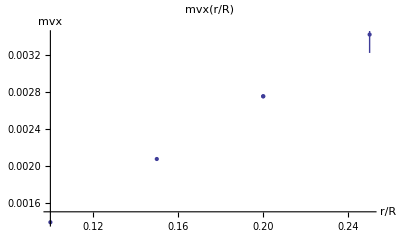
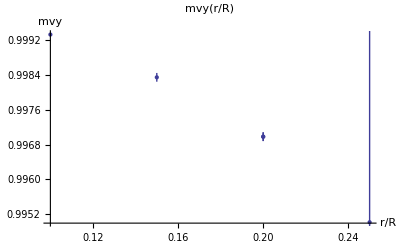
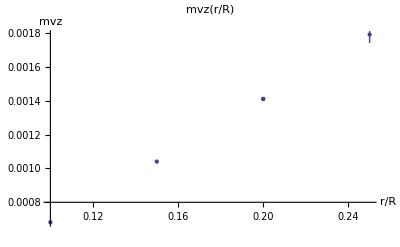
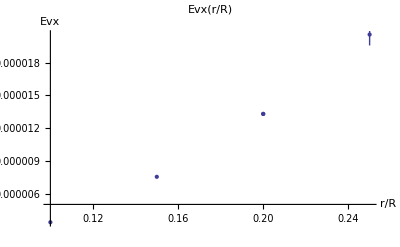
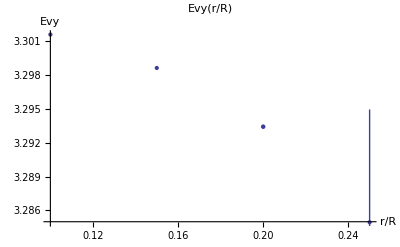
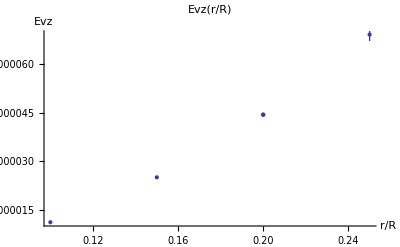
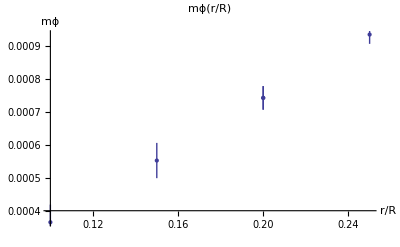

```mathematica
ShowDependance["r/R",allfuncs]
```

All data matches (True):

All such parameters={1,2,10,20,30,40,50,100}

{Nxz,Ny,r/R,lfi,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→128,Ny→5,r/R→0.2,lfi→1.,F(r)→r,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№2:{Nxz→10,Ny→4,r/R→0.01,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№3:{Nxz→128,Ny→5,r/R→0.25,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

So constant parameters are:

{Nxz→128,Ny→5,r/R→0.25,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

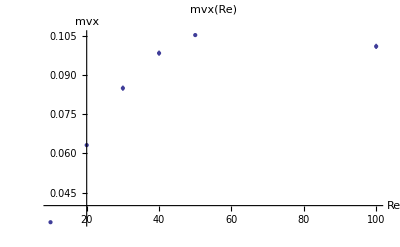
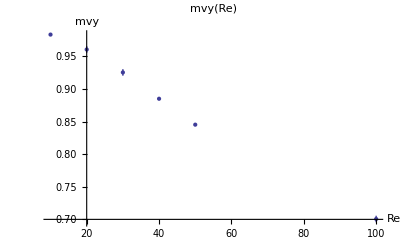
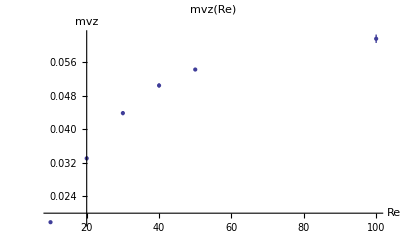
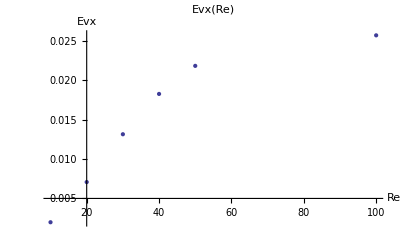
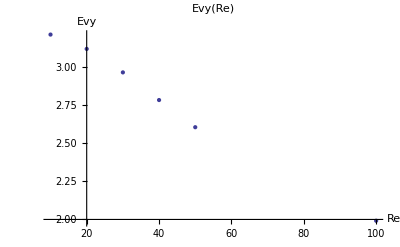
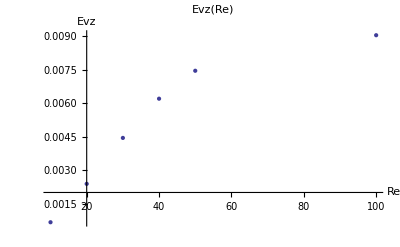
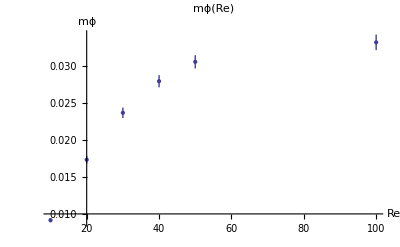

```mathematica
ShowDependance["Re",allfuncs]
```

```mathematica
ShowDependance["lfi",allfuncs]
```

All data matches (True):

All such parameters={0.01,0.1,1,1.,2 π}

{Nxz,Ny,Re,r/R,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→10,Ny→4,Re→1,r/R→0.25,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=4

№2:{Nxz→128,Ny→5,Re→1,r/R→0.2,F(r)→r,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:

{Nxz→10,Ny→4,Re→1,r/R→0.25,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

All data matches (True):

All such parameters={10,20,30,40,50,60,70,80,128}

{Ny,Re,r/R,lfi,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Ny→10,Re→1,r/R→0.25,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=8

№2:{Ny→30,Re→1,r/R→0.25,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№3:{Ny→5,Re→1,r/R→0.2,lfi→1.,F(r)→r,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:

{Ny→10,Re→1,r/R→0.25,lfi→1.,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

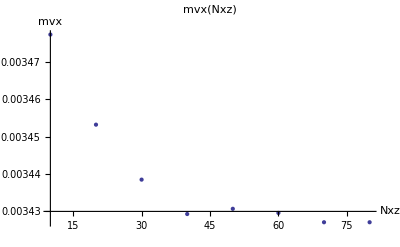
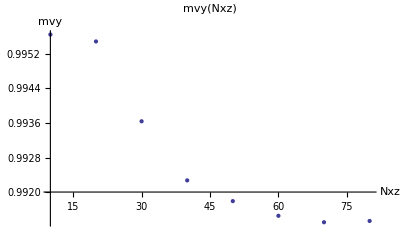
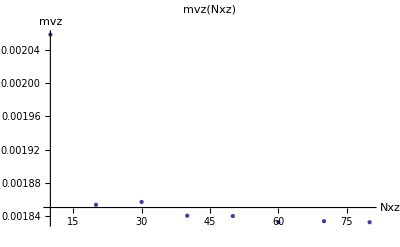
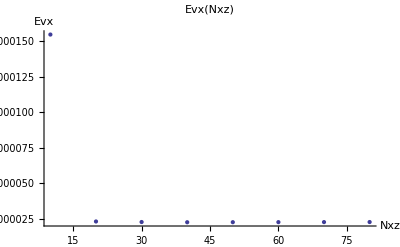
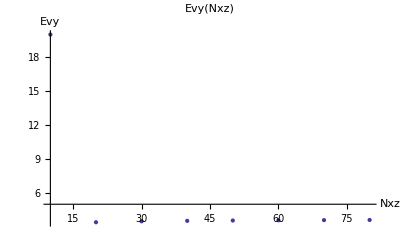
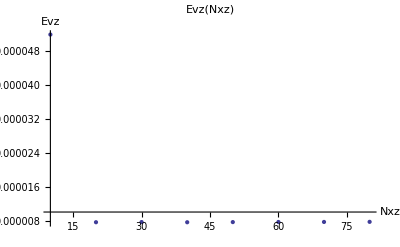
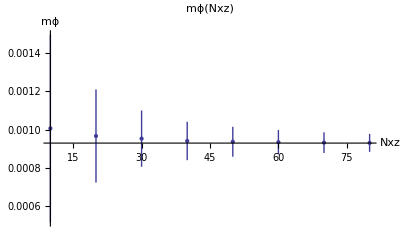

```mathematica
ShowDependance["Nxz",allfuncs]
```

```mathematica
pts//TableForm
```

0.01 | 20.1748
0
 mvx | 0.99565
0
 mvy | 0.0020589
0
 mvz | 3.36935
0
 Evx | 0.0264412
0
 Evy | 6.86602×10^-8
0
 Evz | 3.66375
7.3275
 mϕ | ErrScale 1e-4
0.1 | 0.0034773
0
 mvx | 0.99565
0
 mvy | 0.0020589
0
 mvz | 2.05351×10^-6
0
 Evx | 0.264412
0
 Evy | 6.86604×10^-7
0
 Evz | 0.00100646
0.000488678
 mϕ | ErrScale 1e-4
1. | 0.0034773
0
 mvx | 0.99565
0
 mvy | 0.002059
0
 mvz | 0.000020535
0
 Evx | 2.64412
0
 Evy | 6.86614×10^-6
0
 Evz | 0.00100646
0.000488669
 mϕ | ErrScale 1e-4
2 π | 0.0034773
0
 mvx | 0.99565
0
 mvy | 0.002059
0
 mvz | 0.000129025
0
 Evx | 16.6135
0
 Evy | 0.000043141
0
 Evz | 0.00100646
0.000488669
 mϕ | ErrScale 1e-4

### Отдельное рисование

```mathematica
numfunc=3;
```

```mathematica
list=(Transpose[{First/@pts,{#⟦1⟧,#⟦2⟧}&/@(#[[numfunc]]&/@pts)}];
Transpose[{(1/First[#])&/@pts,First[#]&/@(#[[numfunc]]&/@pts)}]);
```

```mathematica
ListPlot[Drop[list,2],PlotRange->All,PlotLabel->Last[Last[(#1⟦numfunc⟧&)/@pts]],PlotStyle->PointSize[0.03]]
```

```mathematica
Transpose[pts[[All,2;;-2]]]
```

{{{20.1748,0, mvx},{0.0034773,0, mvx},{0.0034773,0, mvx},{0.0034773,0, mvx}},{{0.99565,0, mvy},{0.99565,0, mvy},{0.99565,0, mvy},{0.99565,0, mvy}},{{0.0020589,0, mvz},{0.0020589,0, mvz},{0.002059,0, mvz},{0.002059,0, mvz}},{{3.36935,0, Evx},{2.05351×10^-6,0, Evx},{0.000020535,0, Evx},{0.000129025,0, Evx}},{{0.0264412,0, Evy},{0.264412,0, Evy},{2.64412,0, Evy},{16.6135,0, Evy}},{{6.86602×10^-8,0, Evz},{6.86604×10^-7,0, Evz},{6.86614×10^-6,0, Evz},{0.000043141,0, Evz}},{{3.66375,7.3275, mϕ},{0.00100646,0.000488678, mϕ},{0.00100646,0.000488669, mϕ},{0.00100646,0.000488669, mϕ}}}

```mathematica
With[{param="lfi"},ListPlot[Transpose[{First/@pts,First/@#}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")"]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Transpose[{First/@pts,First/@pts[[All,8]]}]
```

{{0.01,3.66375},{0.1,0.00100646},{1.,0.00100646},{2 π,0.00100646}}

```mathematica
ListPlot[Rest@Transpose[{First/@pts,First/@pts[[All,8]]}]]
```

```mathematica
ListPlot[(First/@pts[[All,5]])]
```

```mathematica
With[{param="Re"},ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Fit[Drop[list,2],{1,x},x]
```

0.990812+2.49089 x